# 19: Least Squares Stability

We are going to fit 100 equally spaced data points on [0,1] using a degree 14 polynomial.

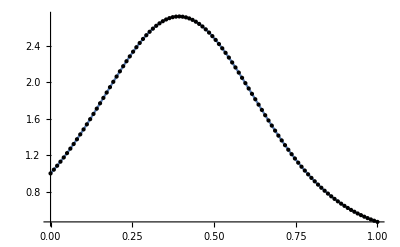

```mathematica
{m,n}={100,15};{a,b}={0.0,1.0};
f[t_]:=Exp[Sin[4t]]
ts=Range[a,b,(b-a)/(m-1)];ys=f[ts];
Plot[ f[x],{x,a,b},Epilog->Point[{ts,ys}ᵀ]]
```

We need to build our least square matrix. We already have the RHS “ys”. The built-in least squares solver does not seem to have any problem.

```mathematica
A=Table[ts⟦i⟧^(j-1),{i,m},{j,n}]/.Indeterminate->1;
xBuiltIn=LeastSquares[A,ys]
```

Power::indet: Indeterminate expression 0.^0 encountered.

{1.00001,3.99348,8.45434,-12.5163,149.202,-1642.39,8801.38,-32945.5,85181.4,-147581.,170033.,-128654.,61470.2,-16819.7,2006.79}

In contrast, a hand-crafted normal equation version does.

```mathematica
xNormalEq = LinearSolve[Aᵀ.A,Aᵀ.ys]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{100.,50.,33.5017,25.2525,20.3034,17.0042,14.6479,12.8809,11.5067,10.4076,«5»},«9»,«5»} may contain significant numerical errors.

{0.999939,4.01889,7.05864,18.4902,-217.689,996.982,-3636.01,7174.4,-5612.21,-2051.96,5619.52,-612.789,-3949.8,2917.74,-658.283}

You might wonder (briefly I hope) which is better

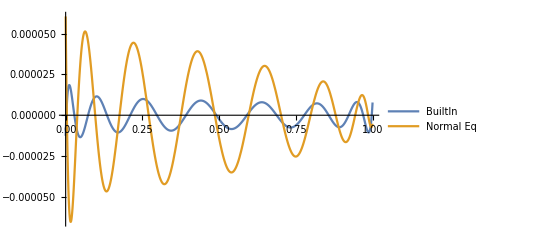

```mathematica
BuiltInPoly[t_]:=Sum[xBuiltIn⟦j⟧ t^(j-1),{j,n}]
NormalEqPoly[t_]:=Sum[xNormalEq⟦j⟧ t^(j-1),{j,n}]
Plot[{f[t]-BuiltInPoly[t],f[t]-NormalEqPoly[t]},{t,a,b},
PlotLegends->{"BuiltIn","Normal Eq"}]
```

The explanation is actually pretty simple. In the normal equations we built a “bad” matrix.

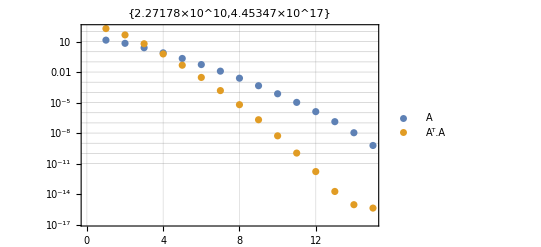

```mathematica
{σsA,σsAtA}=Map[ SingularValueList[#,Tolerance->0]&,{A, Aᵀ.A}];
ListLogPlot[ {σsA,σsAtA},
Frame->True,
PlotLabel->{σsA⟦1⟧/σsA⟦-1⟧,σsAtA⟦1⟧/σsAtA⟦-1⟧},
PlotLegends->{"A","Aᵀ.A"},
GridLines->{Automatic,Table[1.0 10^i,{i,-11,5}]}]
```